```mathematica
solarElectronNumberDensityData=Import["桌面/GitHub/neon/solar_e_density.dat"][[6;;1768]];
solarElectronNumberDensity=Interpolation[solarElectronNumberDensityData];
```

```mathematica
NA=6.02*10^23;(*Avogadro's number: mol^-1*)
GF=1.166*10^-23;(*Fermi constant: eV^-2*)
perVoltoElectronVoltCubic=(1.239*10^-4)^3;(*cm^-3 to eV^3*)
θ12=ArcSin[Sqrt[0.846]]/2;
Δm21=0.753*10^-4;
c=2.99*10^10;(*light speed cm/s*)
Rsun=6.963*10^5;(*solar radius km*)
dimCorrection=2.99*10^10*6.528*10^-22/(6.963*10^10);(*convert c/R_sun into MeV*)
eVtoInverseKm=(1.239*10^-9)^-1;(*convert eV to 1/km*)
```

```mathematica
Pee[L_,Ev_]:=1-Sin[2θ12]^2Sin[(Δm21 L*eVtoInverseKm)/(4Ev*10^6)]^2;
```

```mathematica
SchrodingerRHS[Ev_]:=Δm21/(4Ev*10^6)*eVtoInverseKm*({{-Cos[2θ12], Sin[2θ12]}, {Sin[2θ12], Cos[2θ12]}}).{ve[x],vμ[x]};
```

```mathematica
Ev=10;
schrodingereqs=SchrodingerRHS[Ev];
schsol=NDSolve[{I ve'[x]==schrodingereqs[[1]],I vμ'[x]==schrodingereqs[[2]],ve[0]==1,vμ[0]==0},{ve,vμ},{x,0,40000}];
```

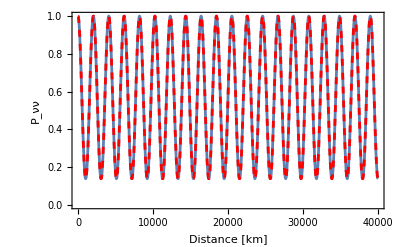

```mathematica
Plot[Evaluate[{ve[x]*Conjugate[ve[x]]}/.schsol],{x,0,40000},FrameLabel->{"Distance [km]",Subscript[P, νν]},Frame->True]~Show~Plot[Pee[x,10],{x,0,40000},PlotStyle->{Red,Dashed,Thickness[.005]}]
```

```mathematica
E^solarElectronNumberDensity[0.9]
```

0.193595

```mathematica
ne[x_]:=If[0.01<=x/Rsun<=0.999,Sqrt[2]*GF*E^solarElectronNumberDensity[x/Rsun]*NA*perVoltoElectronVoltCubic*eVtoInverseKm,0];
Heff[Ev_]:=Δm21/(2Ev*10^6)*eVtoInverseKm*{-Sin[2θ12],0,Cos[2θ12]}-ne[x]{0,0,1};
PolarizationV={px[x],py[x],pz[x]};
LHS=D[PolarizationV,x];
RHS[Ev_]:=Cross[PolarizationV,Heff[Ev]];
```

```mathematica
Ev=10;
rhseqs=RHS[Ev];
sol=NDSolve[{LHS[[1]]==rhseqs[[1]],LHS[[2]]==rhseqs[[2]],LHS[[3]]==rhseqs[[3]],px[0.01Rsun]==0,py[0.01Rsun]==0,pz[0.01Rsun]==1},{px,py,pz},{x,0.01Rsun,2Rsun}]
```

{{px→                                        6
InterpolatingFunction[{{6963., 1.3926 10 }}, <>],py→                                        6
InterpolatingFunction[{{6963., 1.3926 10 }}, <>],pz→                                        6
InterpolatingFunction[{{6963., 1.3926 10 }}, <>]}}

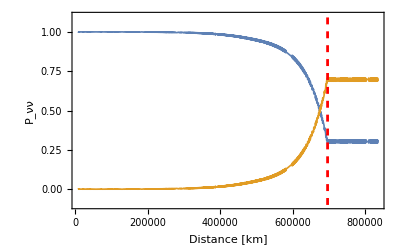

```mathematica
Plot[Evaluate[{0.5(1+pz[x]),0.5(1-pz[x])}/.sol],{x,0.01Rsun,1.2Rsun},FrameLabel->{"Distance [km]",Subscript[P, νν]},Frame->True,PlotStyle->Thickness[.003],PlotRange->All]~Show~ListPlot[{{Rsun,-0.1},{Rsun,1.1}},Joined->True,PlotStyle->{Red,Dashed,Thickness[.005]}]
```

```mathematica
nveff[r_,Rv_:10,Lv_:10^51,EveAvg_:11,EvebAvg_:16]:=1.66*10^32(1-Sqrt[1-(Rv/r)^2])^2(10/Rv)^2*((Lv/10^51)/(EveAvg/10)-(Lv/10^51)/(EvebAvg/10))(*nv number density cm^-3*);
hNS[Rv_,MNS_,Tmatt_]:=0.052*(Rv/10)^2(1.4/MNS)*(Tmatt/1);
nbprime[r_,Rv_:10,MNS_:1.4,Tmatt_:2]:=1.63*10^36 Exp[-(r-Rv)/hNS[Rv,MNS,Tmatt]]
nb[r_,Rv_:10,S_:140,MNS_:1.4]:=4.2*10^30/2*11*(MNS/1.4)^3*(10/r)^3*(100/S)^4
```

```mathematica
Hvv[Ev_,θ_:θ12,Δm2_:Δm21]:=0.5*eVtoInverseKm*({{-Δm2/(2Ev*10^6)Cos[2θ]+Sqrt[2]GF(nb[x])perVoltoElectronVoltCubic, Δm2/(2Ev*10^6)Sin[2θ]+Sqrt[2]GF nveff[x]perVoltoElectronVoltCubic}, {Δm2/(2Ev*10^6)Sin[2θ]+Sqrt[2]GF nveff[x]perVoltoElectronVoltCubic, Δm2/(2Ev*10^6)Cos[2θ]-Sqrt[2]GF(nb[x])perVoltoElectronVoltCubic}}).{ve[x],vμ[x]}
```

```mathematica
Ev=10;
initialFlavor={1,0};
eqsHPsi=Hvv[Ev];
solSN=NDSolve[{I ve'[x]==eqsHPsi[[1]],I vμ'[x]==eqsHPsi[[2]],ve[10]==Sqrt[initialFlavor[[1]]],vμ[10]==Sqrt[initialFlavor[[2]]]},{ve,vμ},{x,10.5,10.9}];
```

```mathematica
Plot[Evaluate[{ve[x]*Conjugate[ve[x]]}/.solSN],{x,10.5,10.9}]
```

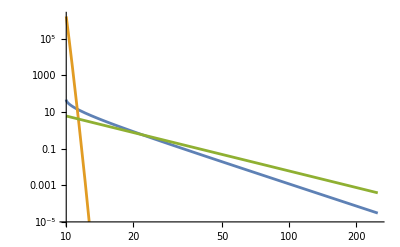

```mathematica
LogLogPlot[{nveff[r]/10^30,nbprime[r]/10^30,nb[r]/10^30},{r,10,250},PlotRange->{10^-5,Automatic}]
```

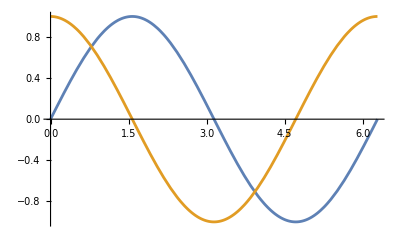

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi}]
```

```mathematica
Sin[x+Pi/2]
```

Cos[x]

```mathematica
Integrate[Cos[x]Sin[x],{x,0,Pi}]
```

0

```mathematica
Cos[ArcSin[x]]
```

√(1-x^2)

```mathematica
Integrate[1-b x,{x,Sqrt[1-(R/r)^2],1}]
```

1-√(1-R^2/r^2)-b (1/2+1/2 (-1+R^2/r^2))

```mathematica
FullSimplify[%]
```

1-(b R^2)/(2 r^2)-√(1-R^2/r^2)

```mathematica
Cos[ArcSin[x]]
```

√(1-x^2)

```mathematica
Integrate[Sqrt[1-(R/r)^2Sin[x]^2]Cos[x]Sin[x],{x,0,ArcSin[R/r]}]
```

(r^4+(-r^4+R^4) √(1-R^4/r^4))/(3 r^2 R^2)

```mathematica
Integrate[1-x,{x,1,Sqrt[1-(R/r)^2]}]
```

-1/2+√(1-R^2/r^2)+1/2 (-1+R^2/r^2)

```mathematica
FullSimplify[%]
```

-1+R^2/(2 r^2)+√(1-R^2/r^2)

```mathematica
Expand[(1-Sqrt[1-(R/r)^2])^2]
```

2-R^2/r^2-2 √(1-R^2/r^2)